Version Date: 11 May 2026

# Kinetic Rate of Reaction and Neural Network Tutorial

## Objective

Apply neural network to kinetic rate of reaction problem

Learn how to use Euler method to solve Ordinary Differential Equation

Learn how to build a simple neural network that has physical law encode in it (the neural network parameter weight has physical meaning)

## Supplement Reading

Quick review of rate of reaction: Kinetics: Initial Rates and Integrated Rate Laws by 
Professor Dave Explains YouTube https://www.youtube.com/watch?v=wYqQCojggyM&t=24s

Neural Network overview: Chapter 11 of Introduction to Machine Learn by Etienne Bernard https://www.wolfram.com/language/introduction-machine-learning/deep-learning-methods/

Euler Method: https://en.wikipedia.org/wiki/Euler_method

## References

Autonomous Discovery of Unknown Reaction Pathways from Databy Chemical Reaction Neural Network  by Weiqi Ji and Sili Deng https://pubs-acs-org.avoserv2.library.fordham.edu/doi/10.1021/acs.jpca.0c09316

Reaction of FD&C Blue 1 with Sodium Percarbonate: Multiple Kinetics Methods Using an Inexpensive Light Meter by Ruth E. Nalliah https://pubs-acs-org.avoserv2.library.fordham.edu/doi/10.1021/acs.jchemed.8b00589

Advancing towards Modeling 2.0 with neural-ODE via Wolfram Language by James Lu https://community.wolfram.com/groups/-/m/t/2386093

## Tutorial Content

Stage 1: Apply Euler method on first order reaction A→B without neural network

Stage 2: Apply Euler method on first order reaction A→B with neural network

Stage 3: Apply model created on Stage 2 on Blue1+H2O2 → product reaction from Physical Chemistry 2 Lab

General Procedure
1. Set up parameters
2. Generate data
3. Build Euler step function 
4. Train neural net and or loss function 
5. Compare with true k value

## Stage 1: Apply Euler method on first order reaction A →B without neural network

### 1. Set up parameters

```mathematica
kTrue=0.2 ;(*put a random ktrue for a first order reaction*)
tMax1= 20; 
nPoints=50; 
tGrid1=Range[0,tMax1, tMax1/(nPoints-1)];
```

### 2. Generate data

### Generate data of [A] for 50 time points by using the formula [A]=[A_0]e^-kt

Add 5% Gaussian noise to create noisy data as Ji and Deng’s paper suggested

```mathematica
Adataclean=Exp[-kTrue*tGrid1];
noise1=RandomVariate[NormalDistribution[0,0.05],nPoints];
Adata= Map[Max[#,0]&, Adataclean*(1+noise1)];
```

### 3. Euler Step

The eulerRHS function create a list that contain the rate of change dA/dt and dB/dt with yList is the initial [A] and [B]

Recall that https://www.priyamstudycentre.com/2019/08/chemical-kinetics-half-life.html#google_vignette -Graphics-

The eulerStep1 function update the concentration of [A] and [B] one time step forward where dtEuler is the time step

Euler formula quick review https://matterofmath.com/calculus/eulers-method/

-Graphics-

The function eulerSolve1 apply the initial concentration to eulerStep1 forward 50 times step

```mathematica
eulerRHS[yList_,kVal_]:={-kVal*yList[[1]],kVal*yList[[1]] };

dtEuler=tMax1/(nPoints-1);
eulerStep1[yList_, kVal_]:=yList+dtEuler*eulerRHS[yList,kVal];

nSteps1=nPoints-1;
eulerSolve1[kVal_]:=NestList[eulerStep1[#,kVal]&,{1.0,0.0},nSteps1];
```

Let test if it work!

```mathematica
testSol1=eulerSolve1[kTrue];
Print["Initial [A] concentration:        ",testSol1[[1,1]]]
Print["Final [A]concentration:         ",testSol1[[-1,1]]]
Print["True Final [A] concentration: ",Exp[-kTrue*tMax1]]
Print["Error:              ",Abs[testSol1[[-1,1]]-Exp[-kTrue*tMax1]]]
```

Initial [A] concentration:        1.

Final [A]concentration:         0.0154101

True Final [A] concentration: 0.0183156

Error:              0.00290555

### 4. Build loss function

loss1 compare the value of [A] compute by the Euler step with the real value over 50 time point and give the mean different

Recall that: https://stackoverflow.com/questions/56401346/mean-absolute-error-in-tensorflow-without-built-in-functions -Graphics-

The Do function is doing a gradient descent where it compute the gradient every step to reduce the loss value https://medium.com/data-science/stochastic-gradient-descent-explained-in-real-life-predicting-your-pizzas-cooking-time-b7639d5e6a32

-Graphics-

```mathematica
loss1[kVal_?NumericQ]:=Module[
{pred,predA},
pred=eulerSolve1[kVal];
predA=pred[[All,1]];
Mean[Abs[predA-Adata]](*the average different of Euler step vs synthetic A data*)
];

kLearn=0.5; 
learnRate=0.01; 
nEpochs1= 100; 
lossHistory1=Table[0,{nEpochs1}];

Do[grad=First[Grad[loss1[k],{k}]/. k->kLearn];
kLearn=kLearn-learnRate*grad;
kLearn=Max[kLearn,10^-6];
lossHistory1[[ep]]=loss1[kLearn];
If[Mod[ep,10]==0,
Print["Epoch ",ep,"  k = ",NumberForm[kLearn,4],"  loss = ",NumberForm[lossHistory1[[ep]],3]]]
,{ep,nEpochs1}];
```

Epoch 10  k = 0.4796  loss = 0.15

Epoch 20  k = 0.4573  loss = 0.145

Epoch 30  k = 0.4326  loss = 0.139

Epoch 40  k = 0.4056  loss = 0.131

Epoch 50  k = 0.374  loss = 0.121

Epoch 60  k = 0.3327  loss = 0.105

Epoch 70  k = 0.2891  loss = 0.0826

Epoch 80  k = 0.2134  loss = 0.0273

Epoch 90  k = 0.1966  loss = 0.013

Epoch 10  k = 0.4796  loss = 0.149

Epoch 20  k = 0.4572  loss = 0.144

Epoch 30  k = 0.4326  loss = 0.138

Epoch 40  k = 0.4056  loss = 0.131

Epoch 50  k = 0.374  loss = 0.12

Epoch 60  k = 0.3325  loss = 0.104

Epoch 70  k = 0.2895  loss = 0.0825

Epoch 80  k = 0.2135  loss = 0.0266

Epoch 90  k = 0.1977  loss = 0.0123

Epoch 100  k = 0.1972  loss = 0.0119

Epoch 100  k = 0.1962  loss = 0.0127

### 5. Compare to true k value

```mathematica
Print["True rate constant:",kTrue]
Print["Rate constant k obtain from Euler method and loss function:",kLearn]
Print["Error:",Abs[kLearn-kTrue]/kTrue*100," %"]
```

True rate constant:0.2

Rate constant k obtain from Euler method and loss function:0.197243

Error:1.37839 %

Alright! Now that you have learn how to use Euler Step and build a loss function let’s incorporate neural network to recover true k value from noisy data! Level up +1!

## Stage 2: Apply Euler method on first order reaction A→B with neural network

### 1. Set up parameter

```mathematica
kTrue=0.2 ;(*put a random ktrue for a first order reaction*)
tMax1= 20; 
nPoints=50; 
tGrid1=Range[0,tMax1, tMax1/(nPoints-1)];

dtEuler=tMax1/(nPoints-1);
nSteps1=nPoints-1;
nStepsNN=5;   (*step for neural network in the later section*)
Print["dtEuler:",N[dtEuler]]
```

dtEuler:0.408163

### 2. Generate data

In Stage 1, we assume [A_0] =1. In Stage 2 to increase the amount of training data available, we generate 20 different concentration

The Table function generate data noisy data for both [A] and [B]

the inputStateN and targetStateN are set of data corresponded to the initial concentration and concentration after nStepsNN respectively (for example  inputStateN contain [A_0]  to [A_4]  and targetStageN contain [A_5]  to [A_9].  inputStateN will serve as input and targetStageN  will serves as output for the neural network in the later section)

```mathematica
initialAs=Range[0.1,2.0,0.1];  (*20 starting concentrations*)

inputStatesN={};
targetStatesN={};

Table[a0=ia;
Aclean=a0*Exp[-kTrue*tGrid1];
Bclean=a0*(1-Exp[-kTrue*tGrid1]);
(*5% Gaussian noise like Stage 1 and Ji& Deng paper*)noiseA=RandomVariate[NormalDistribution[0,0.05],nPoints];
noiseB=RandomVariate[NormalDistribution[0,0.05],nPoints];
(*clamp negative concentrations to zero*)Anoisy=Map[Max[#,0]&,Aclean*(1+noiseA)];
Bnoisy=Map[Max[#,0]&,Bclean*(1+noiseB)];
traj=Transpose[{Anoisy,Bnoisy}];
(*nStepsNN-step pairs within each trajectory only*)AppendTo[inputStatesN,traj[[1;;-nStepsNN-1]]];
AppendTo[targetStatesN,traj[[nStepsNN+1;;]]];,{ia,initialAs}];

inputStatesN=Flatten[inputStatesN,1];
targetStatesN=Flatten[targetStatesN,1];
```

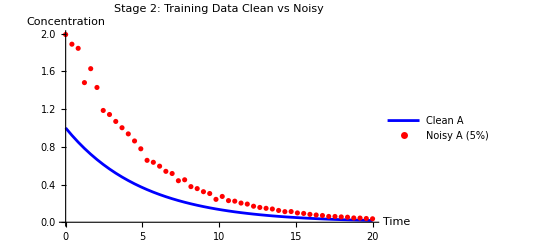

```mathematica
ListPlot[{Transpose[{tGrid1,Exp[-kTrue*tGrid1]}],Transpose[{tGrid1,Anoisy}]},PlotLegends->{"Clean A","Noisy A (5%)"},PlotLabel->"Stage 2: Training Data Clean vs Noisy",AxesLabel->{"Time","Concentration"},Joined->{True,False},PlotStyle->{Blue,Red}]
```

### 3. Build Euler Step with Neural Network

Each of the function below is the neural network version of the Euler function created in Stage 1

eulerRHS  → nnEulerRHS

Here, we want to build a neural network representation of chemical rate law f(y)=W.y where f(y) is the rate of change of each species, W or weight matrix is the 2x2 matrix that encode constant k for each species, and y is [A] and [B] at time t

nnEulerRHS compute f(y)= W.y rate of change by taking in 2 input (y vector that has [A] and [B] at time t)and and output dA/dt and dB/dt

eulerStep1 → eulerStepNet

eulerStepNet is the neural network representation of the concentration in the next time step.

The initial concentration is feed into 1) “rhs” (or nnEulerRHS function) to compute dy (which is dA/dt and dB/dt ) and 2) the “euler” which compute y+dtEuler*dy

The dy computed by “rhs” will be feed to “euler” to finish calculating the output y+dtEuler*dy after one time step

eulerSolve1 → eulerSolveNet

Instead of NestList in eulerSolve1 in Stage 1, use NetNestOperator for neural network in Stage 2

Only use move 5 step forward instead of 50 because during NetTrain backpropagation will not work if it has to do 50 forward and backward because the gradient dtEuler (smaller than zero) is going to be too small (essentially 0 after 50 layers)

```mathematica
nnEulerRHS=NetInitialize@LinearLayer[2,"Input"->2,"Biases"->None]
```

LinearLayer[…]

```mathematica
eulerStepNet=NetGraph[<|"rhs"->nnEulerRHS,"euler"->ThreadingLayer[Function[{y,dy},y+dtEuler*dy],2,"Input"->{"Input1"->{2},"Input2"->{2}}]|>,{NetPort["Input"]->NetPort["euler","Input1"],NetPort["Input"]->"rhs","rhs"->NetPort["euler","Input2"]},"Input"->{2},"Output"->{2}]
```

NetGraph[…]

```mathematica
eulerSolveNet=NetNestOperator[eulerStepNet,nStepsNN]
```

NetNestOperator[…]

### 4. Training the Neutral Network

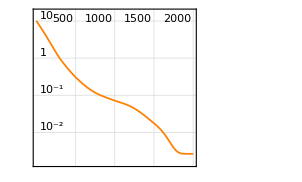
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:30000  rounds:2000  time:7.3min  examples/s:4387
data | ,,  training examples:900  processed examples:1920000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.64×10^-3
 | rounds
loss | -Graphics- | 
 | ]

```mathematica
trainResults=NetTrain[eulerSolveNet,<|"Input"->inputStatesN,"Output"->targetStatesN|>,All,LossFunction->MeanSquaredLossLayer[],MaxTrainingRounds->2000,LearningRate->0.0001,Method->{"ADAM","GradientClipping"->1.0}]
```

```mathematica
finalSolveNet=trainResults["TrainedNet"]
```

NetNestOperator[…]

### 5. Compare to true value k

```mathematica
learnedW=NetExtract[finalSolveNet,{"Net","rhs","Weights"}];
W=Normal[learnedW];
kLearn=-W[[1,1]]
```

```mathematica
Print["True W:"]
{{-kTrue,0},{kTrue,0}}//MatrixForm
Print["Learn W:"]
W//MatrixForm
Print["True k:    ",kTrue]
Print["Learned k: ",kLearn]
Print["Error %:   ",Abs[kLearn-kTrue]/kTrue*100," %"]
```

True W:

(-0.2 | 0
0.2 | 0)

Learn W:

(-0.194598 | 0.000426823
0.192689 | -0.00135173)

True k:    0.2

Learned k: 0.197243

Error %:   1.37839 %

#### Plot

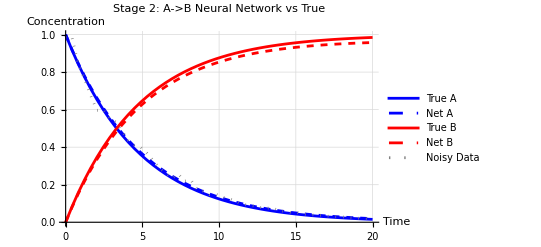

```mathematica
finalStepNet=NetExtract[finalSolveNet,"Net"];
y0test={1,0};
trueTrajectory=eulerSolve1[kTrue];
netTrajectory=NestList[finalStepNet,y0test,nSteps1];
ListLinePlot[{Transpose[{tGrid1,trueTrajectory[[All,1]]}],Transpose[{tGrid1,netTrajectory[[All,1]]}],Transpose[{tGrid1,trueTrajectory[[All,2]]}],Transpose[{tGrid1,netTrajectory[[All,2]]}],Transpose[{tGrid1,Adata}]},PlotLegends->{"True A","Net A","True B","Net B","Noisy Data"},PlotLabel->"Stage 2: A->B Neural Network vs True",AxesLabel->{"Time","Concentration"},PlotStyle->{Blue,{Blue,Dashed},Red,{Red,Dashed},{Gray,Dotted}},GridLines->Automatic]
```

## 3. Apply model created on Stage 2 on Blue1+H2O2 → product reaction from Physical Chemistry 2 Lab (Student Exercise)

Now we have learn how to build neural network to learn and predict k constant  from using concentration of the species and the Euler method, let’s apply it to a experiment in Physical Chemistry Lab 2. 
The key is to follow what the experiment procedure suggested, which is set the [H2O2] 1000
times in excess of the Blue 1 to turn the reaction into a pseudo first order reaction so that we can apply the code in Stage 2. 
Another factor to consider is that different from dtEuler < 1 like the previous example the dtEuler in Stage is large and will effect gradient and loss function so have to reduce nStepNN and scale the dtEuler appropriately. 
Let’s build a neural network to model this reaction!

```mathematica
(*Solution is below but student are encourage to try first*)
```

### 1. Set up parameter

```mathematica
kTrue=0.111;
H2O2conc=0.036;
kObs=kTrue*H2O2conc;
(*r=ktrue[H2O2][Blue] to r=kObs[Blue]for pseudo first reaction*)
```

```mathematica
tMax3=900;
nPoints=50;
tGrid3=Range[0,tMax3,tMax3/(nPoints-1)];
dtEuler=tGrid3[[2]]-tGrid3[[1]];
nSteps=10;

Print["dtEuler:",N[dtEuler]]
```

dtEuler:18.3673

```mathematica
(*because the dtEuler is large, nStepNN (remember dtEuler is apply to eachround)have to be reduced and apply scaling*)
```

```mathematica
nStepsNN=1;
dtScale=tMax3/(nPoints-1);   (* =18.37 seconds per step*)
dtEuler=1.0;                      (*normalized*)

(*rescale kObs to match unit time steps*)
(*in normalized time:kObsScaled=kObs*dtScale*)
kObsScaled=kObs*dtScale;
```

### 2. Generate Data

```mathematica
initialBlue1s=Range[0.1,2.0,0.1];

inputStatesN3={};
targetStatesN3={};

Table[b0=ib;
(*clean analytical solution*)Blue1clean=b0*Exp[-kObsScaled*tGrid3];
Prodclean=b0*(1-Exp[-kObsScaled*tGrid3]);
(*5% Gaussian noise like Stage 1 Stage 2 and Ji& Deng paper*)noiseB=RandomVariate[NormalDistribution[0,0.05],nPoints];
noiseP=RandomVariate[NormalDistribution[0,0.05],nPoints];
(*clamp negative concentrations to zero*)Blue1noisy=Map[Max[#,0]&,Blue1clean*(1+noiseB)];
Prodnoisy=Map[Max[#,0]&,Prodclean*(1+noiseP)];
traj=Transpose[{Blue1noisy,Prodnoisy}];
(*nStepsNN step pairs within each trajectory only*)AppendTo[inputStatesN3,traj[[1;;-nStepsNN-1]]];
AppendTo[targetStatesN3,traj[[nStepsNN+1;;]]];,{ib,initialBlue1s}];

inputStatesN3=Flatten[inputStatesN3,1];
targetStatesN3=Flatten[targetStatesN3,1];
```

### 3. Build Euler Step with Neural Network

```mathematica
nnEulerRHS3=NetInitialize@LinearLayer[2,"Input"->2,"Biases"->None]
eulerStepNet3=NetGraph[<|"rhs"->nnEulerRHS3,"euler"->ThreadingLayer[Function[{y,dy},y+dtEuler*dy],2,"Input"->{"Input1"->{2},"Input2"->{2}}]|>,{NetPort["Input"]->NetPort["euler","Input1"],NetPort["Input"]->"rhs","rhs"->NetPort["euler","Input2"]},"Input"->{2},"Output"->{2}]
eulerSolveNet3=NetNestOperator[eulerStepNet3,nStepsNN]
```

LinearLayer[…]

NetGraph[…]

NetNestOperator[…]

### 4. Train Neural Network

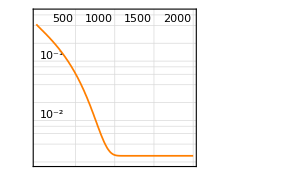
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:32000  rounds:2000  time:29s  examples/s:71896
data | ,,  training examples:980  processed examples:2048000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.54×10^-3
 | rounds
loss | -Graphics- | 
 | ]

```mathematica
trainResults=NetTrain[eulerSolveNet3,<|"Input"->inputStates3,"Output"->targetStates3|>,All,LossFunction->MeanSquaredLossLayer[],MaxTrainingRounds->2000,LearningRate->0.0001,Method->{"ADAM","GradientClipping"->1.0}]
```

```mathematica
finalSolveNet3=trainResults["TrainedNet"]
```

NetNestOperator[…]

```mathematica
learnedW3=NetExtract[finalSolveNet3,{"Net","rhs","Weights"}];
W3=Normal[learnedW3];
learnedKobs=-W3[[1,1]]/dtScale;
learnedKtrue=learnedKobs/H2O2conc;
```

```mathematica
Print["True k:       ",kTrue]
Print["Learned k:    ",learnedKtrue]
Print["k Error %:    ",Abs[learnedKtrue-kTrue]/kTrue*100," %"]
```

True k:       0.111

Learned k:    0.10652

k Error %:    4.03573 %

### Plot

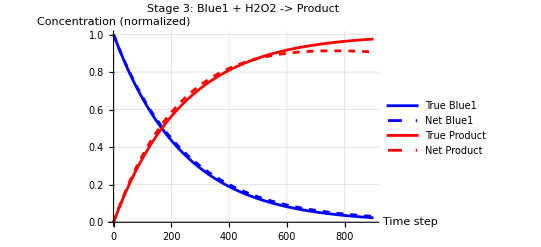

```mathematica
eulerStep3norm[yList_]:=yList+dtEuler*{-kObsScaled*yList[[1]],kObsScaled*yList[[1]]};

trueTrajectory3=NestList[eulerStep3norm,{1,0},nSteps1];
netTrajectory3=NestList[finalStepNet3,{1,0},nSteps1];

ListLinePlot[{Transpose[{tGrid3,trueTrajectory3[[All,1]]}],Transpose[{tGrid3,netTrajectory3[[All,1]]}],Transpose[{tGrid3,trueTrajectory3[[All,2]]}],Transpose[{tGrid3,netTrajectory3[[All,2]]}]},PlotLegends->{"True Blue1","Net Blue1","True Product","Net Product"},PlotLabel->"Stage 3: Blue1 + H2O2 -> Product",AxesLabel->{"Time step","Concentration (normalized)"},PlotStyle->{Blue,{Blue,Dashed},Red,{Red,Dashed}},GridLines->Automatic]
```

## Conclusion

This tutorial provide instruction on how to encode the rate law to the neural network for a simple first order reaction

Next step

Compare to the Julia code in the Ji and Deng’s paper this is a more simple version. The next step can include modifying the code for more complex reaction like ones in the paper.

Encode power law instead of just linear reaction

Increase number of species and reaction

Encode Arrhenius equation for temperature dependent reaction